```mathematica
ClearAll["Global`*"]
```

## Supplementary Material 1 : Quantum Thermal Rectification Under Non-Markovian Dynamics

This notebook includes the modelling and numerical evaluation of the behaviour of a single qutrit coupled to a structured thermal bath.

### Pauli Matrices for Two-Level-System (Qubit)

```mathematica
Subscript[σ, x] = ({{0, 1}, {1, 0}}) ;
```

```mathematica
Subscript[σ, y] = ({{0, -ⅈ}, {ⅈ, 0}});
```

```mathematica
Subscript[σ, z] = ({{1, 0}, {0, -1}});
```

```mathematica
Subscript[σ, I] = ({{1, 0}, {0, 1}});
```

```mathematica
SubPlus[σ] =1/2*(Subscript[σ, x] + ⅈ*Subscript[σ, y]);
```

```mathematica
SubMinus[σ] =1/2*(Subscript[σ, x] - ⅈ*Subscript[σ, y]);
```

There are two energy states in a qubit and they can be described by two column vectors.

```mathematica
Subscript[z, 0]=Transpose[{{0,1}}];
Subscript[z, 1]=Transpose[{{1,0}}];
```

### Pauli Matrix Equivalents for Three-Level-System (Qutrit)/Gell-Mann Matrices

```mathematica
Subscript[ϕ, x] = ({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) ;
Subscript[ϕ, y] = ({{0, -i, 0}, {i, 0, -i}, {0, i, 0}});
Subscript[ϕ, z] =({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Subscript[ϕ, I] = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

There are three energy states in a qutrit and they can be described by three column vectors .

```mathematica
Subscript[Z, 0]=Transpose[{{0,0,1}}];
Subscript[Z, 1]=Transpose[{{0,1,0}}];
Subscript[Z, 2]=Transpose[{{1,0,0}}];
```

### Extended matrices for the 12-dimensional system

```mathematica
Subscript[σ, z,S]=KroneckerProduct[Subscript[ϕ, z],Subscript[σ, I]] ;
Subscript[σ, y,S]=KroneckerProduct[Subscript[ϕ, y],Subscript[σ, I]] ;
Subscript[σ, x,S]=KroneckerProduct[Subscript[ϕ, x],Subscript[σ, I]] ;
Subscript[σ, z,A]=KroneckerProduct[Subscript[ϕ, I],Subscript[σ, z]] ;
Subscript[σ, y,A]=KroneckerProduct[Subscript[ϕ, I],Subscript[σ, y]] ;
Subscript[σ, x,A]=KroneckerProduct[Subscript[ϕ, I],Subscript[σ, x]] ;
```

```mathematica
Subscript[σ, Pos i_]:=Subscript[σ, Pos i]= 1/2*(Subscript[σ, x,i]+ ⅈ Subscript[σ, y,i]);
Subscript[σ, Neg i_]:=Subscript[σ, Neg i]= 1/2*(Subscript[σ, x,i]- ⅈ Subscript[σ, y,i]);
```

### System Hamiltonian

```mathematica
Σ=Subscript[z, 0].Subscript[z, 1] ᵀ;
```

```mathematica
Φ1=Subscript[Z, 0].Subscript[Z, 1] ᵀ;
Φ2=Subscript[Z, 1].Subscript[Z, 2] ᵀ;
```

```mathematica
Subscript[Σ, 01]=KroneckerProduct[Φ1,Subscript[σ, I]] ;
Subscript[Σ, 12]=KroneckerProduct[Φ2,Subscript[σ, I]] ;
Subscript[Σ, A]=KroneckerProduct[Subscript[ϕ, I],Σ] ;
```

```mathematica
Subscript[H, S]=ℏ*Subscript[ω, 01]*Subscript[Σ, 01] ᵀ.Subscript[Σ, 01]+ℏ*(Subscript[ω, 01]+Subscript[ω, 12])*Subscript[Σ, 12] ᵀ.Subscript[Σ, 12];
Subscript[H, A]=ℏ*Subscript[ω, A]*Subscript[Σ, A] ᵀ.Subscript[Σ, A];
Subscript[H, int]=ℏ*κ*((Subscript[Σ, 01]+Subscript[Σ, 12]).Subscript[Σ, A] ᵀ+(Subscript[Σ, 01]+Subscript[Σ, 12])ᵀ.Subscript[Σ, A]);
```

```mathematica
Subscript[H, SA]=Subscript[H, S]+Subscript[H, A]+Subscript[H, int];
```

```mathematica
MatrixForm[Subscript[H, SA]]
```

(ℏ (ω_1+ω_12)+ℏ ω_A | 0 | 0 | 0 | 0 | 0
0 | ℏ (ω_1+ω_12) | κ ℏ | 0 | 0 | 0
0 | κ ℏ | ℏ ω_1+ℏ ω_A | 0 | 0 | 0
0 | 0 | 0 | ℏ ω_1 | κ ℏ | 0
0 | 0 | 0 | κ ℏ | ℏ ω_A | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Subscript[SparseH, SA]=SparseArray[FullSimplify[Subscript[H, SA]]];
```

```mathematica
MatrixForm[Subscript[SparseH, SA]]
```

(ℏ (ω_1+ω_12+ω_A) | 0 | 0 | 0 | 0 | 0
0 | ℏ (ω_1+ω_12) | κ ℏ | 0 | 0 | 0
0 | κ ℏ | ℏ (ω_1+ω_A) | 0 | 0 | 0
0 | 0 | 0 | ℏ ω_1 | κ ℏ | 0
0 | 0 | 0 | κ ℏ | ℏ ω_A | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
{Eval,Evec}=Simplify[Eigensystem[Subscript[SparseH, SA]]];
SparseEvec=SparseArray[Evec];
EvecNormalized=Normalize/@SparseEvec;
list1=FullSimplify[Partition[Riffle[Eval,EvecNormalized],2]];
list1//MatrixForm
```

(0 | SparseArray[…]
ℏ (ω_1+ω_12+ω_A) | SparseArray[…]
1/2 ℏ (ω_1-√(4 κ^2+(ω_1-ω_A)^2)+ω_A) | SparseArray[…]
1/2 ℏ (ω_1+√(4 κ^2+(ω_1-ω_A)^2)+ω_A) | SparseArray[…]
1/2 ℏ (2 ω_1+ω_12-√(4 κ^2+(ω_12-ω_A)^2)+ω_A) | SparseArray[…]
1/2 ℏ (2 ω_1+ω_12+√(4 κ^2+(ω_12-ω_A)^2)+ω_A) | SparseArray[…])

system states and their energies

```mathematica
Subscript[λ, i_]:=Subscript[λ, i]=Transpose[{list1[[i]][[2]]}]
```

```mathematica
HsEVal=Table[list1[[i]][[1]],{i,1,6}]//MatrixForm;
```

## Quantum Master Equation

### Density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, i,j][t],{i,1,6},{j,1,6}];
MatrixForm[%]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t])

### Possible Transition Frequencies

```mathematica
ωMatrix={Flatten[Table[Subscript[ω, {i,j}],{i,1,6},{j,i+1,6}]]}
```

{{ω_{1,2},ω_{1,3},ω_{1,4},ω_{1,5},ω_{1,6},ω_{2,3},ω_{2,4},ω_{2,5},ω_{2,6},ω_{3,4},ω_{3,5},ω_{3,6},ω_{4,5},ω_{4,6},ω_{5,6}}}

```mathematica
ωVals=Flatten[Simplify[Table[(HsEVal[[1,j]]-HsEVal[[1,i]])/ℏ,{i,1,6},{j,i+1,6}]]];
```

```mathematica
Dimensions[ωVals]
```

{15}

### Lindblad Dissipator

```mathematica
Subscript[ℒ, A]=g^2(1-Subscript[n, A][Subscript[ω, A]])(Subscript[Σ, A].ρMatrix[t].Subscript[Σ, A] ᵀ-1/2 Subscript[Σ, A] ᵀ.Subscript[Σ, A].ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, A] ᵀ.Subscript[Σ, A])+(g^2 Subscript[n, A][Subscript[ω, A]](Subscript[Σ, A] ᵀ.ρMatrix[t].Subscript[Σ, A]-1/2 Subscript[Σ, A].Subscript[Σ, A] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[Σ, A].Subscript[Σ, A] ᵀ));
```

### Master Equation

```mathematica
dρ=MatrixForm[Subscript[ℒ, A]-(ⅈ/ℏ(Subscript[SparseH, SA].ρMatrix[t]-ρMatrix[t].Subscript[SparseH, SA]))]
```

(-g^2 (1-n_A[ω_A]) ρ_(1,1)[t]+g^2 n_A[ω_A] ρ_(2,2)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(1,2)[t]-1/2 g^2 n_A[ω_A] ρ_(1,2)[t]-(ⅈ (-ℏ (ω_1+ω_12) ρ_(1,2)[t]+ℏ (ω_1+ω_12+ω_A) ρ_(1,2)[t]-κ ℏ ρ_(1,3)[t]))/ℏ | -g^2 (1-n_A[ω_A]) ρ_(1,3)[t]-(ⅈ (-κ ℏ ρ_(1,2)[t]-ℏ (ω_1+ω_A) ρ_(1,3)[t]+ℏ (ω_1+ω_12+ω_A) ρ_(1,3)[t]))/ℏ+g^2 n_A[ω_A] ρ_(2,4)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(1,4)[t]-1/2 g^2 n_A[ω_A] ρ_(1,4)[t]-(ⅈ (-ℏ ω_1 ρ_(1,4)[t]+ℏ (ω_1+ω_12+ω_A) ρ_(1,4)[t]-κ ℏ ρ_(1,5)[t]))/ℏ | -g^2 (1-n_A[ω_A]) ρ_(1,5)[t]-(ⅈ (-κ ℏ ρ_(1,4)[t]-ℏ ω_A ρ_(1,5)[t]+ℏ (ω_1+ω_12+ω_A) ρ_(1,5)[t]))/ℏ+g^2 n_A[ω_A] ρ_(2,6)[t] | -ⅈ (ω_1+ω_12+ω_A) ρ_(1,6)[t]-1/2 g^2 (1-n_A[ω_A]) ρ_(1,6)[t]-1/2 g^2 n_A[ω_A] ρ_(1,6)[t]
-1/2 g^2 (1-n_A[ω_A]) ρ_(2,1)[t]-1/2 g^2 n_A[ω_A] ρ_(2,1)[t]-(ⅈ (ℏ (ω_1+ω_12) ρ_(2,1)[t]-ℏ (ω_1+ω_12+ω_A) ρ_(2,1)[t]+κ ℏ ρ_(3,1)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(1,1)[t]-g^2 n_A[ω_A] ρ_(2,2)[t]-(ⅈ (-κ ℏ ρ_(2,3)[t]+κ ℏ ρ_(3,2)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(2,3)[t]-1/2 g^2 n_A[ω_A] ρ_(2,3)[t]-(ⅈ (-κ ℏ ρ_(2,2)[t]+ℏ (ω_1+ω_12) ρ_(2,3)[t]-ℏ (ω_1+ω_A) ρ_(2,3)[t]+κ ℏ ρ_(3,3)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(1,3)[t]-g^2 n_A[ω_A] ρ_(2,4)[t]-(ⅈ (-ℏ ω_1 ρ_(2,4)[t]+ℏ (ω_1+ω_12) ρ_(2,4)[t]-κ ℏ ρ_(2,5)[t]+κ ℏ ρ_(3,4)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(2,5)[t]-1/2 g^2 n_A[ω_A] ρ_(2,5)[t]-(ⅈ (-κ ℏ ρ_(2,4)[t]+ℏ (ω_1+ω_12) ρ_(2,5)[t]-ℏ ω_A ρ_(2,5)[t]+κ ℏ ρ_(3,5)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(1,5)[t]-g^2 n_A[ω_A] ρ_(2,6)[t]-(ⅈ (ℏ (ω_1+ω_12) ρ_(2,6)[t]+κ ℏ ρ_(3,6)[t]))/ℏ
-g^2 (1-n_A[ω_A]) ρ_(3,1)[t]-(ⅈ (κ ℏ ρ_(2,1)[t]+ℏ (ω_1+ω_A) ρ_(3,1)[t]-ℏ (ω_1+ω_12+ω_A) ρ_(3,1)[t]))/ℏ+g^2 n_A[ω_A] ρ_(4,2)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(3,2)[t]-1/2 g^2 n_A[ω_A] ρ_(3,2)[t]-(ⅈ (κ ℏ ρ_(2,2)[t]-ℏ (ω_1+ω_12) ρ_(3,2)[t]+ℏ (ω_1+ω_A) ρ_(3,2)[t]-κ ℏ ρ_(3,3)[t]))/ℏ | -(ⅈ (κ ℏ ρ_(2,3)[t]-κ ℏ ρ_(3,2)[t]))/ℏ-g^2 (1-n_A[ω_A]) ρ_(3,3)[t]+g^2 n_A[ω_A] ρ_(4,4)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(3,4)[t]-1/2 g^2 n_A[ω_A] ρ_(3,4)[t]-(ⅈ (κ ℏ ρ_(2,4)[t]-ℏ ω_1 ρ_(3,4)[t]+ℏ (ω_1+ω_A) ρ_(3,4)[t]-κ ℏ ρ_(3,5)[t]))/ℏ | -g^2 (1-n_A[ω_A]) ρ_(3,5)[t]-(ⅈ (κ ℏ ρ_(2,5)[t]-κ ℏ ρ_(3,4)[t]-ℏ ω_A ρ_(3,5)[t]+ℏ (ω_1+ω_A) ρ_(3,5)[t]))/ℏ+g^2 n_A[ω_A] ρ_(4,6)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(3,6)[t]-1/2 g^2 n_A[ω_A] ρ_(3,6)[t]-(ⅈ (κ ℏ ρ_(2,6)[t]+ℏ (ω_1+ω_A) ρ_(3,6)[t]))/ℏ
-1/2 g^2 (1-n_A[ω_A]) ρ_(4,1)[t]-1/2 g^2 n_A[ω_A] ρ_(4,1)[t]-(ⅈ (ℏ ω_1 ρ_(4,1)[t]-ℏ (ω_1+ω_12+ω_A) ρ_(4,1)[t]+κ ℏ ρ_(5,1)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(3,1)[t]-g^2 n_A[ω_A] ρ_(4,2)[t]-(ⅈ (ℏ ω_1 ρ_(4,2)[t]-ℏ (ω_1+ω_12) ρ_(4,2)[t]-κ ℏ ρ_(4,3)[t]+κ ℏ ρ_(5,2)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(4,3)[t]-1/2 g^2 n_A[ω_A] ρ_(4,3)[t]-(ⅈ (-κ ℏ ρ_(4,2)[t]+ℏ ω_1 ρ_(4,3)[t]-ℏ (ω_1+ω_A) ρ_(4,3)[t]+κ ℏ ρ_(5,3)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(3,3)[t]-g^2 n_A[ω_A] ρ_(4,4)[t]-(ⅈ (-κ ℏ ρ_(4,5)[t]+κ ℏ ρ_(5,4)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(4,5)[t]-1/2 g^2 n_A[ω_A] ρ_(4,5)[t]-(ⅈ (-κ ℏ ρ_(4,4)[t]+ℏ ω_1 ρ_(4,5)[t]-ℏ ω_A ρ_(4,5)[t]+κ ℏ ρ_(5,5)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(3,5)[t]-g^2 n_A[ω_A] ρ_(4,6)[t]-(ⅈ (ℏ ω_1 ρ_(4,6)[t]+κ ℏ ρ_(5,6)[t]))/ℏ
-g^2 (1-n_A[ω_A]) ρ_(5,1)[t]-(ⅈ (κ ℏ ρ_(4,1)[t]+ℏ ω_A ρ_(5,1)[t]-ℏ (ω_1+ω_12+ω_A) ρ_(5,1)[t]))/ℏ+g^2 n_A[ω_A] ρ_(6,2)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(5,2)[t]-1/2 g^2 n_A[ω_A] ρ_(5,2)[t]-(ⅈ (κ ℏ ρ_(4,2)[t]-ℏ (ω_1+ω_12) ρ_(5,2)[t]+ℏ ω_A ρ_(5,2)[t]-κ ℏ ρ_(5,3)[t]))/ℏ | -g^2 (1-n_A[ω_A]) ρ_(5,3)[t]-(ⅈ (κ ℏ ρ_(4,3)[t]-κ ℏ ρ_(5,2)[t]+ℏ ω_A ρ_(5,3)[t]-ℏ (ω_1+ω_A) ρ_(5,3)[t]))/ℏ+g^2 n_A[ω_A] ρ_(6,4)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(5,4)[t]-1/2 g^2 n_A[ω_A] ρ_(5,4)[t]-(ⅈ (κ ℏ ρ_(4,4)[t]-ℏ ω_1 ρ_(5,4)[t]+ℏ ω_A ρ_(5,4)[t]-κ ℏ ρ_(5,5)[t]))/ℏ | -(ⅈ (κ ℏ ρ_(4,5)[t]-κ ℏ ρ_(5,4)[t]))/ℏ-g^2 (1-n_A[ω_A]) ρ_(5,5)[t]+g^2 n_A[ω_A] ρ_(6,6)[t] | -1/2 g^2 (1-n_A[ω_A]) ρ_(5,6)[t]-1/2 g^2 n_A[ω_A] ρ_(5,6)[t]-(ⅈ (κ ℏ ρ_(4,6)[t]+ℏ ω_A ρ_(5,6)[t]))/ℏ
ⅈ (ω_1+ω_12+ω_A) ρ_(6,1)[t]-1/2 g^2 (1-n_A[ω_A]) ρ_(6,1)[t]-1/2 g^2 n_A[ω_A] ρ_(6,1)[t] | g^2 (1-n_A[ω_A]) ρ_(5,1)[t]-g^2 n_A[ω_A] ρ_(6,2)[t]-(ⅈ (-ℏ (ω_1+ω_12) ρ_(6,2)[t]-κ ℏ ρ_(6,3)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(6,3)[t]-1/2 g^2 n_A[ω_A] ρ_(6,3)[t]-(ⅈ (-κ ℏ ρ_(6,2)[t]-ℏ (ω_1+ω_A) ρ_(6,3)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(5,3)[t]-g^2 n_A[ω_A] ρ_(6,4)[t]-(ⅈ (-ℏ ω_1 ρ_(6,4)[t]-κ ℏ ρ_(6,5)[t]))/ℏ | -1/2 g^2 (1-n_A[ω_A]) ρ_(6,5)[t]-1/2 g^2 n_A[ω_A] ρ_(6,5)[t]-(ⅈ (-κ ℏ ρ_(6,4)[t]-ℏ ω_A ρ_(6,5)[t]))/ℏ | g^2 (1-n_A[ω_A]) ρ_(5,5)[t]-g^2 n_A[ω_A] ρ_(6,6)[t])

## Solving Master Equation

```mathematica
NBEassum=Subscript[n, q_][ω_]-> 1/(ⅇ^((ℏ ω)/(Subscript[k, B] Subscript[T, q]))+1);
```

### Solving Master Equation

```mathematica
RHS=Subscript[ℒ, A]-(ⅈ/ℏ(Subscript[SparseH, SA].ρMatrix[t]-ρMatrix[t].Subscript[SparseH, SA]));
```

```mathematica
LHS=D[ρMatrix[t], t];
MatrixForm[%]
```

(ρ_(1,1)'[t] | ρ_(1,2)'[t] | ρ_(1,3)'[t] | ρ_(1,4)'[t] | ρ_(1,5)'[t] | ρ_(1,6)'[t]
ρ_(2,1)'[t] | ρ_(2,2)'[t] | ρ_(2,3)'[t] | ρ_(2,4)'[t] | ρ_(2,5)'[t] | ρ_(2,6)'[t]
ρ_(3,1)'[t] | ρ_(3,2)'[t] | ρ_(3,3)'[t] | ρ_(3,4)'[t] | ρ_(3,5)'[t] | ρ_(3,6)'[t]
ρ_(4,1)'[t] | ρ_(4,2)'[t] | ρ_(4,3)'[t] | ρ_(4,4)'[t] | ρ_(4,5)'[t] | ρ_(4,6)'[t]
ρ_(5,1)'[t] | ρ_(5,2)'[t] | ρ_(5,3)'[t] | ρ_(5,4)'[t] | ρ_(5,5)'[t] | ρ_(5,6)'[t]
ρ_(6,1)'[t] | ρ_(6,2)'[t] | ρ_(6,3)'[t] | ρ_(6,4)'[t] | ρ_(6,5)'[t] | ρ_(6,6)'[t])

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,6},{j,1,6}]]]/.Rule->Equal];
```

```mathematica
ωassum1=Flatten[{Table[Subscript[ω, {i,j}]->(-(HsEVal[[1,i]]-HsEVal[[1,j]]))/ℏ,{i,1,6},{j,1,6}]}];
ωassum2={Table[Subscript[ω, i]-> HsEVal[[1,i]]/ℏ,{i,1,6}]};
```

### Initial Conditions

```mathematica
Subscript[ρo, i_]:=Subscript[ρo, i]=Exp[-(ℏ*Subscript[ω, i]*Σᵀ.Σ)/Subscript[T, i]]/Tr[Exp[-(ℏ*Subscript[ω, i]*Σᵀ.Σ)/Subscript[T, i]]];
```

```mathematica
Subscript[ρo, S0]={{0,0,0},{0,0,0},{0,0,1}};
Subscript[ρo, S2]={{1,0,0},{0,0,0},{0,0,0}};
```

### System Parameters

```mathematica
unitassum = {Subscript[k, B]-> 1,ℏ->1,Δ->1};
Subscript[Tassum, 1]={Subscript[ω, 01]->3*Δ,Subscript[ω, 12]->3*Δ,Subscript[ω, A] ->3*Δ,Subscript[T, A]->(1*ℏ*Subscript[ω, 01])/Subscript[k, B],g->0.5*Subscript[ω, A]  ,κ->1*g};
Subscript[Tassum, 5]={Subscript[ω, 01]->3*Δ,Subscript[ω, 12]->3*Δ,Subscript[ω, A] ->3*Δ,Subscript[T, A]->(1*ℏ*Subscript[ω, 01])/Subscript[k, B],g->0.5*Subscript[ω, A]  ,κ->5*g };
Subscript[Tassum, 10]={Subscript[ω, 01]->3*Δ,Subscript[ω, 12]->3*Δ,Subscript[ω, A] ->3*Δ,Subscript[T, A]->(1*ℏ*Subscript[ω, 01])/Subscript[k, B],g->0.5*Subscript[ω, A]  ,κ->10*g };
tmax=((10*ℏ)/(Δ*Subscript[k, B]) )//.Flatten[{Subscript[Tassum, 1],unitassum}];
```

### Solution

Initial conditions with system parameters

```mathematica
Subscript[RHSρoS, 0,λ_]:=KroneckerProduct[Subscript[ρo, S0],Subscript[ρo, A]]//.Flatten[{Subscript[Tassum, λ],unitassum}];(* when qutrit is in Subscript[ρo, S0] *)
Subscript[RHSρoS, 2,λ_]:=KroneckerProduct[Subscript[ρo, S2],Subscript[ρo, A]]//.Flatten[{Subscript[Tassum, λ],unitassum}];(* when qutrit is in Subscript[ρo, S2] *)
```

Set of differential equations with system parameters

```mathematica
Subscript[sol, λ_]:=sol//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}];
```

Solving  differential  equations

```mathematica
Subscript[dynamics, ini_,λ_]:=NDSolve[Flatten[{Subscript[sol, λ]//.Flatten[{NBEassum,Subscript[Tassum, λ],unitassum,ωassum1}],Table[Subscript[ρ, i,j][0]==Subscript[RHSρoS, ini,λ][[i,j]],{i,1,6},{j,1,6}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
```

Density matrix diagonal elements

```mathematica
Subscript[CS, ini_,λ_]:=Flatten[{Table[Subscript[ρ, i,i][t],{i,1,6}]}/. Subscript[dynamics, ini,λ]];
```

Density matrix off-diagonals

```mathematica
Subscript[CSOffD, ini_,λ_]:=Flatten@Table[If[i!=j,Subscript[ρ, i,j][t],Nothing],{i,1,6},{j,1,6}]/. Subscript[dynamics, ini,λ];
```

## Results

### Density Matrix Element Dynamics

plot density matrix diagonals

```mathematica
Subscript[PDiagonalS, ini_,λ_]:=Plot[Evaluate[Subscript[CS, ini,λ]],{t,0,tmax},PlotRange-> All,PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t"],Style["Probability"]}, 
PlotLegends->Automatic,ImageSize->Medium];
```

plot density matrix off-diagonals

```mathematica
Subscript[POffDiagonalS, ini_,λ_]:=Plot[Evaluate[Subscript[CSOffD, ini,λ][[1]]],{t,0,tmax},PlotRange-> All,PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t"],Style["Probability"]}, 
PlotLegends->Automatic,ImageSize->Medium]
```

Density Matrix Element  (Diagonals) Plots

### probabilities

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsRow[{Subscript[PDiagonalS, 0,1],Subscript[PDiagonalS, 0,5],Subscript[PDiagonalS, 0,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals-Initial Condition 1",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsRow[{Subscript[PDiagonalS, 2,1],Subscript[PDiagonalS, 2,5],Subscript[PDiagonalS, 2,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Diagonals-Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

### Coherence

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsRow[{Subscript[POffDiagonalS, 0,1],Subscript[POffDiagonalS, 0,5],Subscript[POffDiagonalS, 0,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off Diagonals-Initial Condition 1",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsRow[{Subscript[POffDiagonalS, 2,1],Subscript[POffDiagonalS, 2,5],Subscript[POffDiagonalS, 2,10]},ImageSize->Full,Epilog->Inset[Style["Density Matrix Off Diagonals-Initial Condition 2",13,Bold],Scaled[{0.5,0.97}]]]
```

-Graphics-

### Qutrit populations derived using partial trace

```mathematica
Subscript[MS, ini_,λ_][t_]:=Table[First[Subscript[ρ, i,j][t]/. Subscript[dynamics, ini,λ]],{i,1,6},{j,1,6}];
```

```mathematica
Subscript[ρSMatrix, ini_,λ_]:=ResourceFunction["MatrixPartialTrace"][Subscript[MS, ini,λ][t],{2},{3,2}];
```

```mathematica
Subscript[QutritDiagonalPlot, ini_,λ_]:=Plot[Evaluate[Diagonal[Subscript[ρSMatrix, ini,λ]]],{t,0,tmax},PlotLegends->{"|2⟩","|1⟩","|0⟩"},PlotLabel->  Style["κ/g=" <> ToString[λ]],AxesLabel->{Style["t"],Style["Probability"]},ImageSize->Medium,PlotRange->Full]
```

With initial condition 1 - RHSρoS_0

```mathematica
GraphicsRow[{Subscript[QutritDiagonalPlot, 0,1],Subscript[QutritDiagonalPlot, 0,5],Subscript[QutritDiagonalPlot, 0,10]},ImageSize->Full]
```

-Graphics-

With initial condition 2 - RHSρoS_2

```mathematica
GraphicsRow[{Subscript[QutritDiagonalPlot, 2,1],Subscript[QutritDiagonalPlot, 2,5],Subscript[QutritDiagonalPlot, 2,10]},ImageSize->Full]
```

-Graphics-

### Trace Distance between qutrit states |0⟩ and |2⟩

```mathematica
Subscript[MSDiff, λ_]:=DiagonalMatrix[Diagonal[Subscript[ρSMatrix, 0,λ]-Subscript[ρSMatrix, 2,λ]]];
Subscript[𝒟, λ_]:=1/2*Tr[MatrixFunction[Sqrt,ConjugateTranspose[Subscript[MSDiff, λ]].Subscript[MSDiff, λ]]];
```

```mathematica
TD1=Plot[Evaluate[Subscript[𝒟, 1]],{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["D(ρ_0, ρ_2)",18.5]},PlotStyle->{RGBColor[0.14,0.8,0.14],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=1",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
TD5=Plot[Evaluate[Subscript[𝒟, 5]],{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["D(ρ_0, ρ_2)",18.5]},PlotStyle->{RGBColor[0.07,0.25,0.6],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=5",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
TD10=Plot[Evaluate[Subscript[𝒟, 10]],{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["D(ρ_0, ρ_2)",18.5]},PlotStyle->{Pink,Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=10",18.5]},{Right,Top}],ImageSize->Large];
```

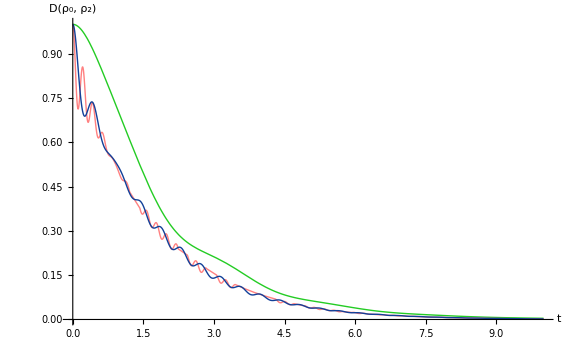

```mathematica
Show[TD1,TD10,TD5]
```

### Time Derivative of Trace Distance

```mathematica
Subscript[ρSMatrix1, ini_,λ_][t_]:=ResourceFunction["MatrixPartialTrace"][Subscript[MS, ini,λ][t],{2},{3,2}];
```

```mathematica
Subscript[MSDiff1, λ_][t_]:=DiagonalMatrix[Diagonal[Subscript[ρSMatrix1, 0,λ][t]-Subscript[ρSMatrix1, 2,λ][t]]];
Subscript[𝒟1, λ_][t_]:=1/2*Tr[MatrixFunction[Sqrt,ConjugateTranspose[Subscript[MSDiff1, λ][t]].Subscript[MSDiff1, λ][t]]];
```

```mathematica
Subscript[TD1, λ_]:=(Subscript[𝒟1, λ][t+0.01]-Subscript[𝒟1, λ][t])/0.01
```

```mathematica
Subscript[TD1, 1];
PlotTD1=Plot[%,{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{RGBColor[0.14,0.8,0.14],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=1",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
Subscript[TD1, 5];
PlotTD5=Plot[%,{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{RGBColor[0.07,0.25,0.6],Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=5",18.5]},{Right,Top}],ImageSize->Large];
```

```mathematica
Subscript[TD1, 10];
PlotTD10=Plot[%,{t,0,tmax},PlotRange->All,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["t",20],Style["σ(t,ρ_(0, 2)(0))",18.5]},PlotStyle->{Pink,Thickness[Large]},PlotLegends-> Placed[{Style["κ/g=10",18.5]},{Right,Top}],ImageSize->Large];
```

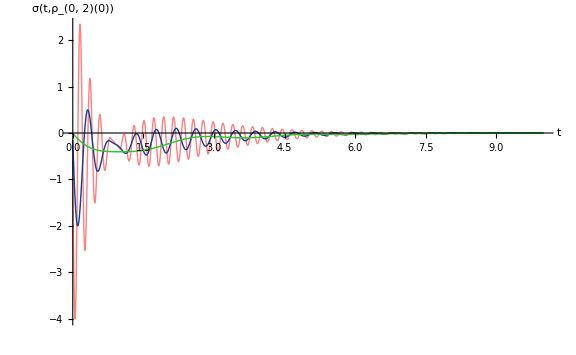

```mathematica
Show[PlotTD10,PlotTD5,PlotTD1]
```

### Total amount of information backflow

```mathematica
InfoBackFlow[ω01_,ω12_,ωA_,TA_,intg_,intκ_,unitassum_]:=
Module[{temp,fnRHSρoS0,fnRHSρoS1,fnsol,fndynamicsS1,fndynamicsS0,fnMS0,fnMS1,fnρSOMatrix1,fnρS1Matrix1,fnMSDiff1,fn𝒟1,fnTD1,fnPlotTD1,fnpts1,fnnlm1},
temp=Flatten[{ωassum1,ωassum2,NBEassum,Subscript[ω, 01]->ω01,Subscript[ω, 12]->ω12,Subscript[ω, A] ->ωA,Subscript[T, A]->TA*Subscript[ω, A],g->intg*Subscript[ω, A] ,κ->intκ*g}];
fnRHSρoS0=KroneckerProduct[Subscript[ρo, S0],Subscript[ρo, A]]//.Flatten[{temp,unitassum}];
fnRHSρoS1=KroneckerProduct[Subscript[ρo, S2],Subscript[ρo, A]]//.Flatten[{temp,unitassum}];
fnsol=sol//.Flatten[{NBEassum,temp,unitassum,ωassum1}];

fndynamicsS1=NDSolve[Flatten[{fnsol//.Flatten[{NBEassum,temp,unitassum,ωassum1}],N[Table[Subscript[ρ, i,j][0]==fnRHSρoS1[[i,j]],{i,1,6},{j,1,6}]]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];
fndynamicsS0=NDSolve[Flatten[{fnsol//.Flatten[{NBEassum,temp,unitassum,ωassum1}],N[Table[Subscript[ρ, i,j][0]==fnRHSρoS0[[i,j]],{i,1,6},{j,1,6}]]}],Flatten[Table[Subscript[ρ, i,j],{i,1,6},{j,1,6}]],{t,0,tmax}];

fnMS0[t_]:=Table[First[Subscript[ρ, i,j][t]/.fndynamicsS0],{i,1,6},{j,1,6}];
fnMS1[t_]:=Table[First[Subscript[ρ, i,j][t]/.fndynamicsS1],{i,1,6},{j,1,6}];
     fnρSOMatrix1[t_]:=ResourceFunction["MatrixPartialTrace"][fnMS0[t],{2},{3,2}];
fnρS1Matrix1[t_]:=ResourceFunction["MatrixPartialTrace"][fnMS1[t],{2},{3,2}];
fnMSDiff1[t_]:=DiagonalMatrix[Diagonal[fnρSOMatrix1[t]-fnρS1Matrix1[t]]];
fn𝒟1[t_]:=1/2*Tr[MatrixFunction[Sqrt,ConjugateTranspose[fnMSDiff1[t]].fnMSDiff1[t]]];
fnTD1=(fn𝒟1[t+0.01]-fn𝒟1[t])/0.01;
fnPlotTD1=Plot[fnTD1,{t,0,5},PlotRange->Full,PlotStyle->Blue,PlotLabel->  Style["κ/g"],AxesLabel->{Style["t(s)"],Style["(ⅆ𝒟 (SubscriptBox[ρ, 1], SubscriptBox[ρ, 2]))/ⅆt"]}];
fnpts1=Cases[fnPlotTD1,Line[dat_]:>dat,All]//Flatten[#,1]&;
fnnlm1=Quiet[NonlinearModelFit[fnpts1,a*Exp[-b*x]*Cos[ω*x+φ]+c,{a,b,ω,φ,c},x]];
{fnnlm1["BestFitParameters"],fnnlm1["EstimatedVariance"],Total[Differences[fnpts1[[All,1]]]*MovingAverage[Clip[fnpts1[[All,2]],{0,∞}],2]]}
]
```

```mathematica
PlotInfoBackFlow[ω01_,ω12_,ωA_,TA_,intg_,κmin_,κmax_,κres_,unitassum_]:=
Module[{tempx,tempy,temp,model1},
tempx=Table[{κ},{κ,κmin,κmax,κres}];
tempy=Table[{Abs[InfoBackFlow[ω01,ω12,ωA,TA,intg,intκ,unitassum][[3]]]},{intκ,κmin,κmax,κres}];
temp=Table[{MapThread[List,{tempx[[;;,1]],tempy[[;;,1]]}]}];
ListPlot[temp,AxesStyle->Directive[Darker[Gray],15.5],AxesLabel->{Style["κ/g",20],Style["∫_(σ > 0) σ(t,ρ_(0, 2)(0))ⅆt",15]},Joined->True,PlotStyle->{RGBColor[0,0.44,0.44]},ImageSize->Medium]
]
```

```mathematica
TotalInfo=PlotInfoBackFlow[3,3,3,1,0.5,0.01,5,0.01,unitassum];
```

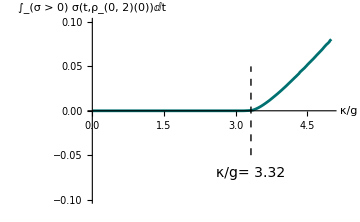

```mathematica
Show[TotalInfo,Graphics[{Black,Dashed,Line[{{3.32,-0.05},{3.32,0.05}}],Text[Style["κ/g= 3.32",14,Black],{3.32,-0.07},{0,0}]}],PlotRange->{All,{-0.1,0.1}}]
```